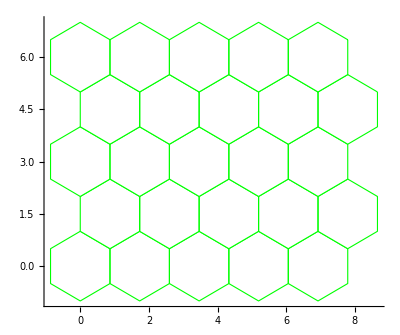

```mathematica
(*定义一个画正六边形的函数*)drawHexagon[x_,y_,r_]:={EdgeForm[{Green}],FaceForm[White],Polygon[Table[{x+r Cos[theta],y+r Sin[theta]},{theta,Pi/6,2 Pi,Pi/3}]]}

(*设置半径和行/列数量*)
r=1;
rows=5;
cols=5;

(*计算基础向量的长度*)
dx=r Sqrt[3];(*与前面结论相符*)dy=1.5*r;(*与前面结论相符*)(*初始化画图列表*)graphicList={};

(*循环遍历行和列，添加正六边形*)
For[j=0,j<rows,j++,For[i=0,i<cols,i++,(*计算偏移量，第一行为基准*)x=i dx;
y=j dy;
(*奇数行正六边形中心需要偏移 dx/2*)If[OddQ[j],x+=dx/2];
(*添加到画图列表*)AppendTo[graphicList,drawHexagon[x,y,r]];]]

(*生成图形*)
Graphics[graphicList,Axes->True]
```